## Density - dependent loss in lattice tubes

### Setup

```mathematica
SetOptions[#,PlotRange->All,Axes->False,Frame->True,LabelStyle->{FontFamily->"Helvetica",FontSize->14}]&/@{Plot,LogPlot,LogLogPlot,ContourPlot};
SetOptions[#,PlotStyle->{Thick,Red}]&/@{Plot,LogPlot,LogLogPlot};
```

### Calculation parameters

```mathematica
Parameters={
(* fundamental constants *)
h->6.626070040*^-34,
kB->1.38064852*^-23,
amu->1.660539040*^-27,
ℏ->h/(2Pi),

(* atomic constants *)
m->88 amu,

(* unit conversions *)
mWcm2->10,
gauss->1*^-4,

Kee->4.0*^-18 ,(* two-body loss coefficient in m^3/s, Lisdat, PRL 103, 090801 *)
Keg->5.3*^-19,
Kdep->3.2*^-16
};
```

```mathematica
LatticeWavelength=914*^-9;
AreaLattice=Pi(160.*^-6 240*^-6)/4;
AreaLatticeSite=(LatticeWavelength/2)^2;
AreaPixel=(5.4*^-6)^2;
TotalAtomNumber=5*^5;

Sites=AreaLattice/AreaLatticeSite;
SitesPerPixel=AreaPixel/AreaLatticeSite;

(*NSite=TotalAtomNumber/Sites;*)
NSite=0.86;
NPixel=TotalAtomNumber/(AreaLattice/AreaPixel);

RadialTrapFrequency=2Pi 110*^3;
LongitudinalTrapFrequency=2Pi 200;
LongitudinalTemperature=2*^-6;
```

### Two-body loss from ee collisions in a lattice tube

two-body loss coefficient from Lisdat 2009 PRL

Atomic density for a single atom trapped in a lattice tube, assuming that the radial x,y axes are in the harmonic oscillator ground state, and that the longitudinal axis is at temperature Tz.

```mathematica
Density[x_,y_,z_]:=(m ωr)/(π ℏ)*Exp[-(m ωr(x^2+y^2))/ℏ]*Sqrt[m ωz^2/(2 kB Tz)]/Sqrt[π]*Exp[-(m ωz^2 z^2)/(2kB Tz)];
```

Check density normalization to number of particles per tube

```mathematica
Integrate[Density[x,y,z],{x,-Infinity,Infinity},{y,-Infinity,Infinity},{z,-Infinity,Infinity},Assumptions->{m>0,ωr>0,ℏ>0,ωz>0,kB>0,Tz>0}]
```

1

Show atomic density distribution along tube and corresponding loss rate assuming that a single atom is in a site is in the excited state

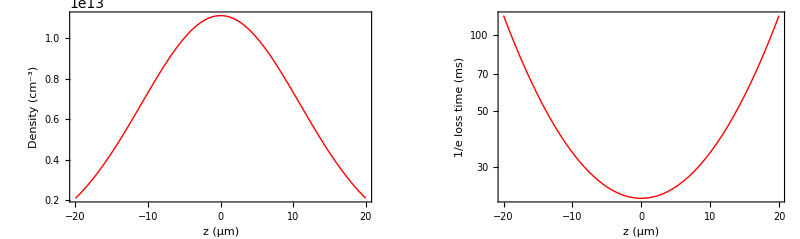

```mathematica
TrapParameters={ωr->RadialTrapFrequency,ωz->LongitudinalTrapFrequency,Tz->LongitudinalTemperature};
rep=Join[Parameters,TrapParameters];

GraphicsRow[{
Plot[1*^-6 Density[0,0,z 1*^-6]//.rep,
{z,-20,20},
FrameLabel->{"z (μm)","Density (cm^-3)"}],
LogPlot[1*^3/(Kee Density[0,0,z 1*^-6])//.rep,
{z,-20,20},
FrameLabel->{"z (μm)", "1/e loss time (ms)"}]
},ImageSize->Full]
```

### Spectroscopy parameters: Rabi frequency and shifts

Magnetic field shifts from measured Sr-88 clock Poli, 2014

```mathematica
SecondOrderZeemanShift[MagneticField_]:=-2.33*^7 *MagneticField^2;(*-23.3 Hz/mT^2*)
LightShift[Intensity_]:=-1.8*^-3*Intensity;(* -18 Hz/ W/cm^2*)
```

Induced Rabi frequency as function of magnetic field and clock laser intensity. This is the number quoted in the 2006 PRL by Oates, Hollberg, et al.

```mathematica
RabiFrequency88[Intensity_,MagneticField_]:=2Pi 198 * MagneticField*Sqrt[Intensity/10];
```

For our values, what do we get?

```mathematica
Block[{
int=133.*^3 mWcm2/81,
B=40gauss},
Print["Rabi frequency = ",RabiFrequency88[int, B]/(2Pi)//.Parameters," Hz"];
Print["Rabi pi time = ",1*^3Pi/RabiFrequency88[int, B]//.Parameters," ms"];
Print["Zeeman shift = ",SecondOrderZeemanShift[B]//.Parameters," Hz"];
Print["Light shift = ",LightShift[int]//.Parameters, " Hz"];
];
```

Rabi frequency = 32.0929 Hz

Rabi pi time = 15.5798 ms

Zeeman shift = -372.8 Hz

Light shift = -29.5556 Hz

```mathematica
2
```

2

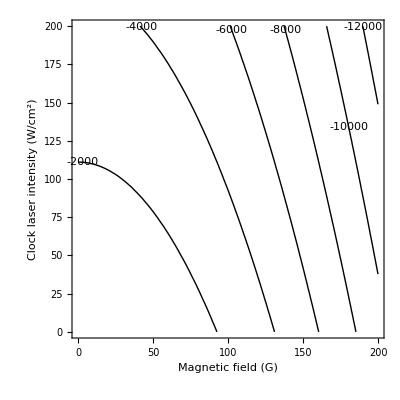

```mathematica
ContourPlot[(SecondOrderZeemanShift[b gauss]+LightShift[i 1*^3 mWcm2]//.rep),{b,0,200},{i,0,200},ContourLabels->True,ContourShading->None,FrameLabel->{"Magnetic field (G)", "Clock laser intensity (W/cm^2)"}]
```

### Rabi spectroscopy in presence of loss

Use model derived first in PRL 103, 090801 (2009) to model Sr-88 spectra, and then also used in PRA 84, 052716 (2011) to model Sr-87 spectra. We are going to ignore the questionable e-g loss coefficient found in the first paper, but otherwise we will use the same model, but simplify it to remove trap loss and dephasing collisions.

```mathematica
RabiHamiltonian[MagneticField_,Intensity_,Detuning_]:={
{0, RabiFrequency88[Intensity,MagneticField]/2},
{RabiFrequency88[Intensity,MagneticField/2], Detuning}
};
Dissipator[DensityMatrix_]:=Module[{
γee=(NSite*Kee Density[0,0,0]//.rep),
γeg=(NSite*Keg Density[0,0,0]//.rep),
γdep=(NSite*Kdep Density[0,0,0]//.rep)
},
-{
{γeg DensityMatrix[[2,2]]DensityMatrix[[1,1]],
γeg(DensityMatrix[[1,1]]+DensityMatrix[[2,2]])DensityMatrix[[1,2]]/2+γee DensityMatrix[[2,2]]DensityMatrix[[1,2]]/2+
γdep DensityMatrix[[1,1]]DensityMatrix[[1,2]]
},
{γeg(DensityMatrix[[1,1]]+DensityMatrix[[2,2]])DensityMatrix[[2,1]]/2+
γee DensityMatrix[[2,2]]DensityMatrix[[2,1]]/2+
γdep DensityMatrix[[1,1]]DensityMatrix[[2,1]],
γeg DensityMatrix[[2,2]]DensityMatrix[[1,1]]+γee DensityMatrix[[2,2]]^2}
}];
```

```mathematica
MakeDensityMatrix[Symbol_,Argument_]:=Table[Subscript[Symbol,i,j][Argument],{i,2},{j,2}];

Vectorize[Matrix_]:=Flatten[Matrix];
MatrixToEquationList[lhs_,rhs_]:=Thread[Vectorize[lhs]==Vectorize[rhs]];
```

```mathematica
VonNeumannEquation[MagneticField_,Intensity_,Detuning_]:=Module[{
R=MakeDensityMatrix[ρ,t],
Rdot=D[MakeDensityMatrix[ρ,t],t],
H=RabiHamiltonian[MagneticField,Intensity,Detuning]
},
Join[MatrixToEquationList[Rdot,-I(R.H-H.R)+Dissipator[R]][[{1,2,4}]],
{Subscript[ρ,1,1][0]==1,
Subscript[ρ,1,2][0]==0,
Subscript[ρ,2,2][0]==0}]/.{Subscript[ρ,2,1][t]->Conjugate[Subscript[ρ,1,2][t]]}
];
```

```mathematica
eqn=VonNeumannEquation[200. gauss,133000.mWcm2/81,0]//.rep;
%//TableForm
```

ρ_(1,1)'[t]==-ⅈ (-504.114 Conjugate[ρ_(1,2)[t]]+504.114 ρ_(1,2)[t])-5.06736 ρ_(1,1)[t] ρ_(2,2)[t]
ρ_(1,2)'[t]==-3059.54 ρ_(1,1)[t] ρ_(1,2)[t]-ⅈ (504.114 ρ_(1,1)[t]-504.114 ρ_(2,2)[t])-19.1221 ρ_(1,2)[t] ρ_(2,2)[t]-2.53368 ρ_(1,2)[t] (ρ_(1,1)[t]+ρ_(2,2)[t])
ρ_(2,2)'[t]==-ⅈ (504.114 Conjugate[ρ_(1,2)[t]]-504.114 ρ_(1,2)[t])-5.06736 ρ_(1,1)[t] ρ_(2,2)[t]-38.2442 (ρ_(2,2)[t])^2
ρ_(1,1)[0]==1
ρ_(1,2)[0]==0
ρ_(2,2)[0]==0

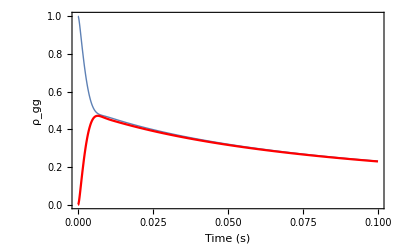

```mathematica
sol=NDSolve[eqn,{Subscript[ρ,1,1],Subscript[ρ,2,2]},{t,0,1}];
Show[
Plot[Evaluate[{Subscript[ρ,1,1][t],Subscript[ρ,2,2][t]}/.sol],{t,0,.1},
FrameLabel->{"Time (s)","ρ_gg"},PlotRange->{All,{0,1}}]
(*Plot[1/(1+(NSite Kee Density[0,0,0]//.rep)t),{t,0,1},PlotStyle->{Thick,Black}]*)
]
(*Show[
LogLogPlot[Evaluate[{Subscript[ρ,1,1][t],Subscript[ρ,2,2][t]}/.sol],{t,0,1},
FrameLabel->{"Time (s)","ρ_gg"},PlotRange->{All,{0,1}}]
(*LogLogPlot[1/(1+(NSite Kee Density[0,0,0]//.rep)t),{t,0,1},PlotStyle->{Thick,Black}]*)
]*)
```

So let’s assume that the OBE reaches steady state for all times and that the excited state loss simply acts on that steady state. This seems like a reasonable model given the above results. We have to compare to the data to see if it makes sense, though.

```mathematica
DSolve[{ne'[t]==-k ne[t]^2,ne[0]==1},ne[t],t]
```

{{ne[t]→1/(1+k t)}}

```mathematica
(NSite Kee Density[0,0,0]//.rep)
```

38.2442